存储对象

Wolfram 语言可以很容易地将东西储存在 Wolfram Cloud，或者储存在你的计算机系统本地。让我们先来谈谈 Wolfram Cloud。

在 Wolfram Cloud 中，所有东西都是一个云对象，由 UUID(通用唯一识别码，universally unique identifier)来指定。

云对象会立即被分配一个 UUID：

```mathematica
CloudObject[ ]
```

CloudObject[]

一旦你创建了一个云对象，它就会被分配一个很长的随机生成的 UUID。UUID 的好处是，我们可以假设永远不会生成两个相同的 UUID。(一共有300 万亿万亿万亿个可能的 Wolfram UUID。)

将 Wolfram 语言表达式放入云中：

```mathematica
CloudPut[{-Graphics-,-Graphics-}]
```

CloudObject[]

从云端拿回表达式：

```mathematica
CloudGet[%]
```

{-Graphics-,-Graphics-}

如果你已经使用 = 和 := 进行了定义，你可以使用 CloudSave 来保存这些定义。(如果你的定义依赖于其他定义，这些定义也会被保存。)你可以使用 CloudGet 来将你的定义加载到新的会话中。

创建一个定义：

```mathematica
colorlist[n_Integer]:=RandomColor[n]
```

将其保存在云中，以便以后使用 CloudGet 进行读取：

```mathematica
CloudSave[colorlist]
```

CloudObject[]

CloudPut 允许你存储一个 Wolfram 语言表达式。但是，如果你想逐步积累来自 Wolfram 语言内部的表达式，或者来自外部设备或传感器的表达式，该怎么办？

Wolfram Data Drop 正是让你完成这一点。你首先要创建一个数据仓。你可以在 Wolfram 语言中使用 CreateDatabin 来完成。

创建一个数据仓：

```mathematica
bin=CreateDatabin[ ]
```

Databin[…]

你可以从各种外部设备和服务来将数据添加到这个数据仓中，也可以使用 Wolfram 语言中的 DatabinAdd。

向数据仓中添加一个条目：

```mathematica
DatabinAdd[bin,{1,2,3,4}]
```

Databin[…]

向同一个数据仓中添加另一个条目：

```mathematica
DatabinAdd[bin,{a,b,c}]
```

Databin[]

获取存储在数据仓中的值：

```mathematica
Values[bin]
```

{{1,2,3,4},{a,b,c}}

这是从我桌子上的一个小传感器积累的数据的数据仓。DateListPlot 将绘制出数据的时间序列。

使用一个短 ID 来引用连接到我桌子上的传感器的数据仓：

```mathematica
Databin["7m3ujLVf"]
```

Databin[…]

使用数据仓来绘制时间序列：

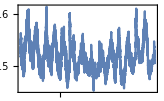
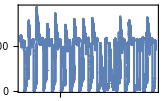
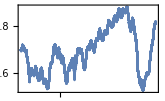
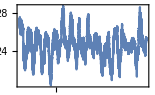
<|humidity→-Graphics-,light→-Graphics-,pressure→-Graphics-,temperature→-Graphics-|>

```mathematica
DateListPlot[Databin["7m3ujLVf"]]
```

Wolfram Data Drop，像 CloudPut 和 CloudSave 一样，将数据保存在云端。但是，特别是如果你没有连接到云端时，你可能反而想在本地计算机中存储对象。如果你弄清了你想把文件放在文件系统的位置，你可以使用 Put、Save 和 Get 来进行存储和读取。

也可以让 Wolfram 语言自动计算出一个“匿名”的本地位置。你可以使用 LocalObject 来完成此功能。

生成一个“匿名”位置，用于 Put、Save 等等：

```mathematica
LocalObject[ ]
```

LocalObject[file:///Users/sw/Library/Wolfram/Objects/365e034d-9830-4842-8681-75d3714b3d19]

把一个图像放到这个位置：

```mathematica
Put[-Graphics-,%]
```

LocalObject[file:///Users/sw/Library/Wolfram/Objects/365e034d-9830-4842-8681-75d3714b3d19]

取回图像：

```mathematica
Get[%]
```

-Graphics-

词汇

CloudObject[ ] |   | 创建一个云对象
CloudPut[expr] |   | 写入云
CloudGet[obj] |   | 从云端取出
CloudSave[s] |   | 将定义保存到云端
Databin["id"] |   | 存放累积数据的数据仓
CreateDatabin[ ] |   | 创建数据仓
DatabinAdd[obj,value] |   | 将对象添加到数据仓
DateListPlot[data] |   | 绘制日期列表图
LocalObject[ ] |   | 创建本地对象
Put[expr,obj] |   | 放入本地对象
Get[obj] |   | 从本地对象中取出

问&答

UUID 中的字母和数字是什么意思？

它们是十六进制的数字；字母“a”到“f”是十六进制中的数字 10 到 15。每个 UUID 有32个十六进制数字，对应 16^32≈3×10^38 种可能性。

UUID 的可能数量与现实中的对象相比如何？

这大约是一立方公里水中包含的原子数，或宇宙中恒星数量的 100 万亿倍。如果地球上 500 亿台电脑中的每一台都以 10 GHz 的频率生成 UUID，那么耗尽 UUID 也需要宇宙的年龄那么久。

UUID 与短 ID 如何关联？

所有由 URLShorten 生成的短 ID 都是明确注册的，并保证是唯一的，有点像互联网上的域名。UUID 足够长，所以即使没有任何形式的中心注册，也可以假定它们是唯一的。

我可以在 CloudObject、CloudPut 中指定文件名吗？

是的。文件名将被认为是相对于你在云中的主目录。该文件还将获得一个 URL，其中包括你所使用的云的基础地址，以及你的用户 ID。

其他人可以访问我存储在云对象中的内容吗？

通常不可以。但如果你设置了 Permissions→"Public" 选项，那么每个人就都可以访问它，就像我们在第 36 节中讨论的网络应用一样。你还可以准确地定义你想让谁来做什么。

我可以在不使用 Wolfram 语言的情况下使用数据仓吗？

是的，你可以使用网络和许多其他系统来创建并添加数据仓。

有没有一种方法可以在云端操作一个表达式，而不需要获得整个表达式？

有的。让它成为一个云表达式(使用 CreateCloudExpression)。然后，所有获取和设置一部分表达式的常规方法都可以正常使用，但表达式将永远存储在云端。

技术笔记

当你使用云端时，Wolfram 笔记本文档会在你每一次修改后自动保存，除非你指定不要这样做。

你可以用 DumpSave 来比 Save 更有效地保存大型对象，但这样你创建的是二进制文件，而不是文本文件。

LocalCache[CloudObject[...]] 是一种引用云对象的方式，如果有其内容的本地缓存的话，就可以使用(如果没有的话，将进行创建)。

数据仓可以有数据签名，指定其中的数据应该如何解释，例如在单位、日期格式等方面。

像 x=3 这样的赋值只在 Wolfram 语言会话期间存在。但你可以使用 PersistentValue["x"]=3 这样的东西来存储具有不同程度的持续性的值(在一台计算机上；无论何时登录；在一定时间内；等等)。

探索更多

Wolfram 语言中的文件操作指南 »

Wolfram Data Drop »